```mathematica
Clear["Global`*"]
Nblevels=4;
ReH={{0,Re[Ωp]/2,0,Re[ΩL]/2},{Re[Ωp]/2,0,Re[Ωm]/2,0},{0,Re[Ωm]/2,0,Re[Ωc]/2},{Re[ΩL]/2,0,Re[Ωc]/2,0}};
ImH={{0,(-Im[Ωp])/2,0,(-Im[ΩL])/2},{Im[Ωp]/2,0,(-Im[Ωm])/2,0},{0,Im[Ωm]/2,0,Im[Ωc]/2},{Im[ΩL]/2,0,-Im[Ωc]/2,0}};

Reρρ[t_]=Table[Reρ[i,j][t],{i,Nblevels},{j,1,Nblevels}];
Do[
Reρ[i,j][t]=Reρ[j,i][t],
{i,Nblevels},{j,1,i-1}
];

Imρρ[t_]=Table[Imρ[i,j][t],{i,Nblevels},{j,1,Nblevels}];
Do[
Imρ[i,j][t]=-Imρ[j,i][t],
{i,Nblevels},{j,1,i-1}
];

Do[Imρ[i,i][t]=0,{i,1,Nblevels}];
Delta =- DiagonalMatrix[{0,Δp,Δp+Δm,Δp+Δm-Δc}];
(*Delta =- DiagonalMatrix[{0,Δp,0,0}];*)
ReH=ReH+Delta;
Delta//MatrixForm;
ReH//MatrixForm;
ImH//MatrixForm;
(*Total Hamiltonian*)
TotalH=ReH+ⅈ ImH//MatrixForm;
ReB=(ReH.Imρρ[t]-Imρρ[t].ReH)+(ImH.Reρρ[t]-Reρρ[t].ImH);
ImB=-(ReH.Reρρ[t]-Reρρ[t].ReH)+(ImH.Imρρ[t]-Imρρ[t].ImH);

GammaSpont=IdentityMatrix[Nblevels];
GammaSpont[[1,1]]=0;
GammaSpont[[2,2]]=γ;
GammaSpont[[3,3]]=γ;
GammaSpont[[4,4]]=Γ;


ReLoss=-1/2(GammaSpont.Reρρ[t]+Reρρ[t].GammaSpont);
ReLoss//MatrixForm;
ImLoss=-1/2(GammaSpont.Imρρ[t]+Imρρ[t].GammaSpont);
ImLoss//MatrixForm;

ReLoss[[1,1]]=ReLoss[[1,1]]+γ Reρ[2,2][t]+Γ Reρ[4,4][t];
ReLoss[[4,4]]=ReLoss[[4,4]]+γ Reρ[3,3][t];


For[ii=1, ii≤ 4, ii++,
If[ii≠ 2,
ReLoss[[2,ii]]-= γ2d Reρ[2,ii][t];
ReLoss[[ii,2]]-= γ2d Reρ[2,ii][t];
ImLoss[[ii,2]]-=γ2d Imρ[ii,2][t];
ImLoss[[2,ii]]+=γ2d Imρ[ii,2][t];
]
]

For[ii=1, ii≤ 4, ii++,
If[ii≠ 3,
ReLoss[[3,ii]]-= γ3d Reρ[3,ii][t];
ReLoss[[ii,3]]-= γ3d Reρ[3,ii][t];
ImLoss[[ii,3]]-=γ3d Imρ[ii,3][t];
ImLoss[[3,ii]]+=γ3d Imρ[ii,3][t];
]
]
ReLoss//MatrixForm;
ReA=FullSimplify[ReB+ReLoss];
ImA=FullSimplify[ImB+ImLoss];
ReA//MatrixForm;
(ReB+ReLoss)//MatrixForm;
eqnsDifRe2=Flatten[
Table [
Simplify[ReA[[i,j]]==0,(Reρ[i,j][t])∈Reals&&(Imρ[i,j][t])∈Reals&&(Reρ[j,i][t])∈Reals&&(Imρ[j,i][t])∈Reals],
{i,1,Nblevels},{j,i,Nblevels}
]
];
eqnsDifIm1=Flatten[Table [Simplify[ImA[[i,j]]==0,(Reρ[i,j][t])∈Reals&&(Imρ[i,j][t])∈Reals&&(Reρ[j,i][t])∈Reals&&(Imρ[j,i][t])∈Reals],{i,1,Nblevels},{j,i+1,Nblevels}]];
eqnstime=Join[eqnsDifRe2,eqnsDifIm1];
eqnstime[[1]];
VariablesSolve2=Join[
Flatten[Table[(Reρ[i,i][t]),{i,1,Nblevels}]],
Flatten[Table[(Reρ[i,j][t]),{i,1,Nblevels},{j,i+1,Nblevels}]],
Flatten[Table[(Imρ[i,j][t]),{i,1,Nblevels},{j,i+1,Nblevels}]]];

variablesList=Table[
{ii,VariablesSolve2[[ii]]},
{ii,1,Length[VariablesSolve2]}
];
variablesList//TableForm;
MatrixCoef2=CoefficientArrays[eqnstime,VariablesSolve2];
MM2=Normal[MatrixCoef2][[2]];
Y2=-Normal[MatrixCoef2][[1]];
eqnsDifRe2check=MM2.VariablesSolve2;
ReA[[1,1]];
eqnsDifRe2check[[1]];
Coef2=Simplify[ReA[[1,1]]/eqnsDifRe2check[[1]]];
MM2=MM2*Coef2;
Y2=Y2*Coef2;
Y2[[1]]=1;
MM2[[1]]=Table[0,{i,1,Length[VariablesSolve2]}];
MM2[[1]][[1;;Nblevels]]=Table[1,{i,1,Nblevels}];
MM2//MatrixForm;
Y2//MatrixForm;
solution:=LinearSolve[MM2,Y2];
(*ρ1S:=solution[[1]];
ρ2S:=solution[[2]];
ρ3S:=solution[[3]];
ρ4S:=solution[[4]];*)
Imρ12S:=solution[[11]];
Imρ14S:=solution[[13]];
Imρ23S:=solution[[14]];
Imρ34S:=solution[[16]];
Reρ12S:=solution[[5]];
Reρ14S:=solution[[7]];
Reρ23S:=solution[[8]];
Reρ34S:=solution[[10]];
```

```mathematica
σv[T_]=√(kB T/Mat);
fv[v_,T_]=1/(√(2 Pi (σv[T])^2)) Exp[-v^2/(σv[T])^2];
(*Plot[fv[v,300],{v,-600,600}];*)
```

```mathematica
Num1[ΩpIn_,nat_,wz_,ΩmIn_,ΩcIn_,ΔpIn_,ΔmIn_,ΔcIn_,γ2dIn_,γ3dIn_,T_,Nv_]:=Module[
{Iout={},zz=-2.8*wz,Deltazz=wz/20,
Ωpout=10^9 ΩpIn,ΩLSignal=10^9 ΩL0,ΩcCalc=10^9 ΩcIn,ΩmCalc=10^9 ΩmIn,
constA,constB,ProDark,condition,condition2},vsteps=Nv;minv=-0.5σv[T];maxv=0.5σv[T];dv=(maxv-minv)/vsteps;Normv=Integrate[fv[v,T],{v,minv,maxv}];

(* constants used in the calculations*)
constA=nat 1/(ℏ ϵ0 c);
constB=1/2 ϵ0 c ℏ^2;

(* define dephasing parameters *)
γ2d=γ2dIn;
γ3d=γ3dIn;

(* numerically solve 1D equation *)
While[(zz<=(2.8*wz)),


Ωp=Ωpout/10^9;
ΩL=ΩLSignal/10^9;
Ωc=ΩcCalc/10^9;
Ωm=ΩmCalc/10^9;

Do[Δp=ΔpIn-2*π*v0/λp/10^9;
Δc=ΔcIn+2*π*v0/λc/10^9;
Δm=ΔmIn;
(* 319 light/852 light *)
Ωpout=Ωpout-ⅈ *Deltazz*constA d12^2 ωP*(-ⅈ Imρ12S + Reρ12S)*fv[v0,T] dv/Normv;
ΩLSignal=ΩLSignal-ⅈ *Deltazz*constA d14^2 ωL(-ⅈ Imρ14S + Reρ14S)*fv[v0,T] dv/Normv;

(* MW fields, if copropagating *)
ΩmCalc=ΩmCalc-ⅈ *Deltazz*constA d23^2 ωM (-ⅈ Imρ23S + Reρ23S )*fv[v0,T] dv/Normv;

(* 510 light *)
ΩcCalc=ΩcCalc -ⅈ *Deltazz*constA d34^2 ωC (+ⅈ Imρ34S + Reρ34S )*fv[v0,T] dv/Normv,{v0,minv,maxv,dv}];

Iout=AppendTo[Iout,{zz,constB/d14^2  Abs[ΩLSignal]^2,constB/d12^2  Abs[Ωpout]^2,constB/d23^2  Abs[ΩmCalc]^2,constB/d34^2  Abs[ΩcCalc]^2}];

zz=zz+Deltazz];

Iout]
```

```mathematica
Rung1[ΩpIn_,nat_,wz_,ΩmIn_,ΩcIn_,ΔpIn_,ΔmIn_,ΔcIn_,γ2dIn_,γ3dIn_,T_,Nv_]:=Module[
{Iout={},zz=-2.8*wz,Deltazz=wz/20,
Ωpout=10^9 ΩpIn,ΩLSignal=10^9 ΩL0,ΩcCalc=10^9 ΩcIn,ΩmCalc=10^9 ΩmIn,
constA,constB},vsteps=Nv;minv=-0.5σv[T];maxv=0.5σv[T];dv=(maxv-minv)/vsteps;Normv=Integrate[fv[v,T],{v,minv,maxv}];
constA=nat (1/(ℏ ϵ0 c));
constB=(1/2)ϵ0 c ℏ^2;

(* define dephasing parameters *)
γ2d=γ2dIn;
γ3d=γ3dIn;

(* numerically solve 1D equation *)
While[(zz<=(2.8*wz)),


Ωp=Ωpout/10^9;
ΩL=ΩLSignal/10^9;
Ωc=ΩcCalc/10^9;
Ωm=ΩmCalc/10^9;

(*K1*)
Do[Δp=ΔpIn-2*π*v0/λp/10^9;
Δc=ΔcIn+2*π*v0/λc/10^9;
Δm=ΔmIn;

ΩpoutK1=-ⅈ *constA  d12^2 ωP*(-ⅈ Imρ12S + Reρ12S)*fv[v0,T] dv/Normv;
ΩLSignalK1=-ⅈ *constA d14^2 ωL(-ⅈ Imρ14S + Reρ14S)*fv[v0,T] dv/Normv;
ΩmCalcK1=-ⅈ *constA d23^2 ωM (-ⅈ Imρ23S + Reρ23S )*fv[v0,T] dv/Normv;
ΩcCalcK1=-ⅈ *constA d34^2 ωC (+ⅈ Imρ34S + Reρ34S )*fv[v0,T] dv/Normv,{v0,minv,maxv,dv}];

ΩpoutValK1=Ωpout + 0.5 Deltazz ΩpoutK1;
ΩLSignalValK1=ΩLSignal +0.5 Deltazz ΩLSignalK1;
ΩmCalcValK1=ΩmCalc+0.5 Deltazz ΩmCalcK1;
ΩcCalcValK1=ΩcCalc+0.5 Deltazz ΩcCalcK1;

(*K2*)
Ωp=ΩpoutValK1/10^9;
ΩL=ΩLSignalValK1/10^9;
Ωc=ΩcCalcValK1/10^9;
Ωm=ΩmCalcValK1/10^9;


Do[Δp=ΔpIn-2*π*v0/λp/10^9;
Δc=ΔcIn+2*π*v0/λc/10^9;
Δm=ΔmIn;

ΩpoutK2=-ⅈ *constA  d12^2 ωP*(-ⅈ Imρ12S + Reρ12S)*fv[v0,T] dv/Normv;
ΩLSignalK2=-ⅈ *constA d14^2 ωL(-ⅈ Imρ14S + Reρ14S)*fv[v0,T] dv/Normv;
ΩmCalcK2=-ⅈ *constA d23^2 ωM (-ⅈ Imρ23S + Reρ23S )*fv[v0,T] dv/Normv;
ΩcCalcK2=-ⅈ *constA d34^2 ωC (+ⅈ Imρ34S + Reρ34S )*fv[v0,T] dv/Normv,{v0,minv,maxv,dv}];

ΩpoutValK2=Ωpout + 0.5 Deltazz ΩpoutK2;
ΩLSignalValK2=ΩLSignal +0.5 Deltazz ΩLSignalK2;
ΩmCalcValK2=ΩmCalc+0.5 Deltazz ΩmCalcK2;
ΩcCalcValK2=ΩcCalc+0.5 Deltazz ΩcCalcK2;

(*K3*)
Ωp=ΩpoutValK2/10^9;
ΩL=ΩLSignalValK2/10^9;
Ωc=ΩcCalcValK2/10^9;
Ωm=ΩmCalcValK2/10^9;


Do[Δp=ΔpIn-2*π*v0/λp/10^9;
Δc=ΔcIn+2*π*v0/λc/10^9;
Δm=ΔmIn;

ΩpoutK3=-ⅈ *constA  d12^2 ωP*(-ⅈ Imρ12S + Reρ12S)*fv[v0,T] dv/Normv;
ΩLSignalK3=-ⅈ *constA d14^2 ωL(-ⅈ Imρ14S + Reρ14S)*fv[v0,T] dv/Normv;
ΩmCalcK3=-ⅈ *constA d23^2 ωM (-ⅈ Imρ23S + Reρ23S )*fv[v0,T] dv/Normv;
ΩcCalcK3=-ⅈ *constA d34^2 ωC (+ⅈ Imρ34S + Reρ34S )*fv[v0,T] dv/Normv,{v0,minv,maxv,dv}];

ΩpoutValK3=Ωpout +  0.5*Deltazz ΩpoutK3;
ΩLSignalValK3=ΩLSignal + 0.5*Deltazz ΩLSignalK3;
ΩmCalcValK3=ΩmCalc+ 0.5*Deltazz ΩmCalcK3;
ΩcCalcValK3=ΩcCalc+0.5* Deltazz ΩcCalcK3;

(*K4*)
Ωp=ΩpoutValK3/10^9;
ΩL=ΩLSignalValK3/10^9;
Ωc=ΩcCalcValK3/10^9;
Ωm=ΩmCalcValK3/10^9;

Do[Δp=ΔpIn-2*π*v0/λp/10^9;
Δc=ΔcIn+2*π*v0/λc/10^9;
Δm=ΔmIn;

ΩpoutK4=-ⅈ *constA  d12^2 ωP*(-ⅈ Imρ12S + Reρ12S)*fv[v0,T] dv/Normv;
ΩLSignalK4=-ⅈ *constA d14^2 ωL(-ⅈ Imρ14S + Reρ14S)*fv[v0,T] dv/Normv;
ΩmCalcK4=-ⅈ *constA d23^2 ωM (-ⅈ Imρ23S + Reρ23S )*fv[v0,T] dv/Normv;
ΩcCalcK4=-ⅈ *constA d34^2 ωC (+ⅈ Imρ34S + Reρ34S )*fv[v0,T] dv/Normv,{v0,minv,maxv,dv}];

Ωpout=Ωpout + Deltazz ((1/6) ΩpoutK1+(1/3)ΩpoutK2+(1/3)ΩpoutK3+(1/6)ΩpoutK4 );
ΩLSignal=ΩLSignal + Deltazz ((1/6) ΩLSignalK1+(1/3)ΩLSignalK2+(1/3)ΩLSignalK3+(1/6)ΩLSignalK4 );
ΩmCalc=ΩmCalc+Deltazz ((1/6) ΩmCalcK1+(1/3)ΩmCalcK2+(1/3)ΩmCalcK3+(1/6)ΩmCalcK4 );
ΩcCalc=ΩcCalc +Deltazz ((1/6) ΩcCalcK1+(1/3)ΩcCalcK2+(1/3)ΩcCalcK3+(1/6)ΩcCalcK4 );

Iout=AppendTo[Iout,{zz,constB/d14^2  Abs[ΩLSignal]^2,constB/d12^2  Abs[Ωpout]^2,constB/d23^2  Abs[ΩmCalc]^2,constB/d34^2  Abs[ΩcCalc]^2}];
zz=zz+Deltazz];

Iout]
```

### Definition of Parameters

```mathematica
DefineParam1:=Module[{res},ϵ0=8.85*10^(-12);
c=2.9979*10^8;
h=6.626*10^(-34);
elcharge=1.6021766208 10^-19;
a0=0.5292*10^(-10);
Eua=4.36*10^(-18); (*Hartree Energy*)
ℏ=h/(2π);
μm=10^(-6);
Mp=1.6726231*10^-27;Mat=133 Mp;kB=1.3806503*10^-23;
λp=0.319 10^-6;
λc=0.510 10^-6;
λL=0.852 10^-6;
σ0=3 λp^2/(2 π);

wz0=1*10^-3;(*m*)
wp0=50 10^-6;
wc0=47 10^-6;

ωL=2π c/λL;
ωP=2π c/λp;
ωC=2π c/λc;
ωM=2π 9.9 10^9;

Is=16.67;
(*OD0=20;*)
Ip0=2 Is*(Ωp0/γ)^2;
Pp0=π wp0^2 Ip0/2;
(*nat0=OD0/(Sqrt[π/2] wz0 σ0);*)
nat0=OD0/(2 wz0 σ0);

d12=0.003 elcharge a0;
d14=3.162 elcharge a0;
d34=0.025elcharge a0;
d23=1137.443elcharge a0;

Γ=2 π 5.22*10^-3;(*γ=2 π 0.01 10^-3;γ2=γ;γ3=1*γ;γd=2 π 0.1 10^-3;
γ2d=γd;γ3d=γd;*)
(*Ωp0=2 π 0.209 10^-3;Ωm0=2 π *2.01 10^-3;Ωc0=2 π*13.58 10^-3;ΩL0=0;*)

δ0=0*2 π*10^-3;(*δp=0.299412*2 π*10^-3;*)
(*Δp=0.0*2 π*10^-3;Δm=-0.0*2 π*10^-3;Δc=0*2 π*10^-3;*)

(*T0=300;*)
δwd=4 π /λp  σv[T0] √2 √Log[2]/10^9;
(*Nv0=51;*)

res=0;res];
```

### Plot

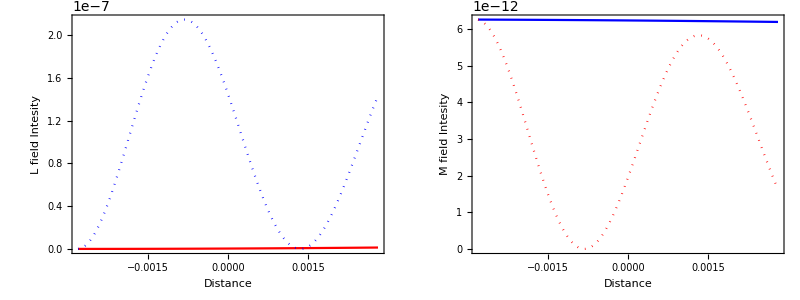

```mathematica
DefineParam1;
Ωp0=2 π 0.0011119*1 10^-3;Ωm0=2 π *0.001 10^-3;Ωc0=2 π*36.58 10^-3;ΩL0=0.0 2 π *6.01 10^-3;OD0=18;γd=2 π 0.001 10^-3;
γ2d=γd;γ3d=γd;γ=2 π 0.01 10^-3;γ2=γ;γ3=1*γ;Δp=0*2 π*10^-3;Δm=-0*2 π*10^-3;Δc=0*2 π*10^-3;
T0=0.00000000001;
Nv0=50;
FigureNum1=fourWaveNum1[Ωp0,OD0*1/2 1/wz0 1/σ0,wz0,Ωm0,Ωc0,Δp,Δm,Δc,γ2d,γ3d,T0,Nv0];
FigureRung1=fourWaveRung1[Ωp0,OD0*1/2 1/wz0 1/σ0,wz0,Ωm0,Ωc0,Δp,Δm,Δc,γ2d,γ3d,T0,Nv0];
p1=ListLinePlot[{FigureRung1[[All,{1,2}]],FigureNum1[[All,{1,2}]]},PlotStyle->{Red,{Blue,Dotted}},ImageSize->Medium,FrameLabel->{{"L field Intesity ",""},{"Distance",""}}];
p2=ListLinePlot[{FigureRung1[[All,{1,4}]],FigureNum1[[All,{1,4}]]},PlotStyle->{Blue,{Red,Dotted}},ImageSize->Medium,FrameLabel->{{"M field Intesity ",""},{"Distance",""}}];
Grid[{{p1,p2}}]
```